```mathematica
μ=0.62;
γ=5/3;
```

```mathematica
years=365.25*86400;
tEnd=10^3 years;
tref:=1/Ω[Rper,zper]
```

```mathematica
rper=0.7Rsun;
θper=45*Pi/180;
kRoss=21.1;
χ=(16*T[Rper,zper]^3*sigmaSB*(γ-1)*μ*mP)/(3*kRoss*ρ[Rper,zper]^2*kB);  (*this is what Goldreich and Schubert call χ*)
ξradiative = (γ-1)*χ;    (*this is what Balbus and Schaan call ξrad*)

ν=23;   (*from Menou&Balbus2004*)

η=596;     (*from Menou&Balbus2004*)
```

```mathematica
ξradiative = (γ-1)*χ ; 
ν=23;  
η=596;    
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=0.01Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

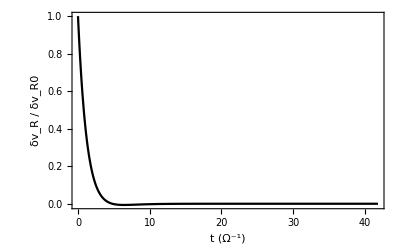

```mathematica
Graphico3=Plot[δvRsol[t*tref]/δvRsol[0],{t,0,(tEnd/tref)/(2*10^3)},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)","δv_R / δv_R0 ","ξ_rad = ξ_(rad⊙),  ν = ν_⊙,  η = η_⊙"},BaseStyle->{FontWeight->"Plain",FontSize->14},FrameStyle->Black, LabelStyle -> Black]
```

```mathematica
ξradiative = (γ-1)*χ ; 
ν=2;  
η=596;     
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=0.01Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

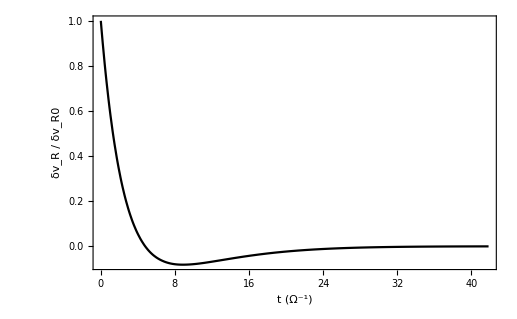

```mathematica
Graphico4=Plot[δvRsol[t*tref]/δvRsol[0],{t,0,(tEnd/tref)/(2*10^3)},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)","δv_R / δv_R0 ", "ξ_rad = ξ_(rad⊙),  ν = 0.1ν_⊙,  η = η_⊙"},BaseStyle->{FontWeight->"Plain",FontSize->14},FrameStyle->Black, LabelStyle -> Black]
```

```mathematica
ξradiative = (γ-1)*χ ; 
ν=0;  
η=596;    
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=0.01Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

```mathematica
Graphico5=Plot[δvRsol[10^5 t]/δvRsol[0],{t,0,(tEnd/10^5)/1000},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{"t (10^5s)","δv_R / δv_R0 "},BaseStyle->{FontWeight->"Plain",FontSize->14},FrameStyle->Black, LabelStyle -> Black];
```

```mathematica
ξradiative = (γ-1)*χ ; 
ν=23;  
η=596;    
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=100Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

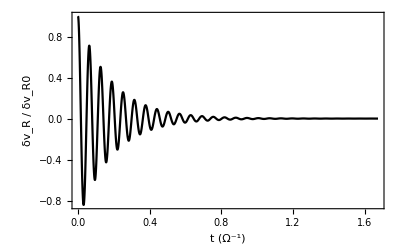

```mathematica
Graphico6=Plot[δvRsol[t*tref]/δvRsol[0],{t,0,(tEnd/tref)/(5*10^4)},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)","δv_R / δv_R0 ", "k·v_A = 10^2Ω,  ξ_rad = ξ_(rad⊙),  ν = ν_⊙,  η = η_⊙"},BaseStyle->{FontWeight->"Plain",FontSize->14},FrameStyle->Black,LabelStyle->Black]
```

```mathematica
ξradiative = (γ-1)*χ ; 
ν=23;  
η=60;     
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=100Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

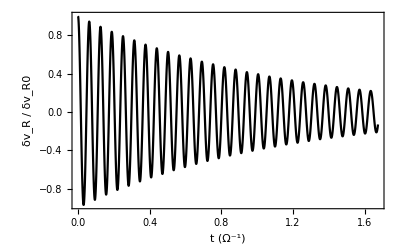

```mathematica
Graphico7=Plot[δvRsol[t*tref]/δvRsol[0],{t,0,(tEnd/tref)/(5*10^4)},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)","δv_R / δv_R0 ","k·v_A = 10^2Ω,  ξ_rad = ξ_(rad⊙),  ν = ν_⊙,  η = 0.1η_⊙"},BaseStyle->{FontWeight->"Plain",FontSize->14},FrameStyle->Black, LabelStyle -> Black]
```

```mathematica
(*Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\NiceExamples\\pic3.png",Graphico3,ImageResolution->180];
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\NiceExamples\\pic4.png",Graphico4,ImageResolution->180];
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\NiceExamples\\pic6.png",Graphico6,ImageResolution->180];
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\NiceExamples\\pic7.png",Graphico7,ImageResolution->180];*)
```

```mathematica
θper=35*Pi/180;
ξradiative = (γ-1)*χ ; 
ν=23;  
η=596;    
kR0=-8*10^-8;
kϕ0=5*10^-8;
kz0=-2*10^-7;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=0.0001Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

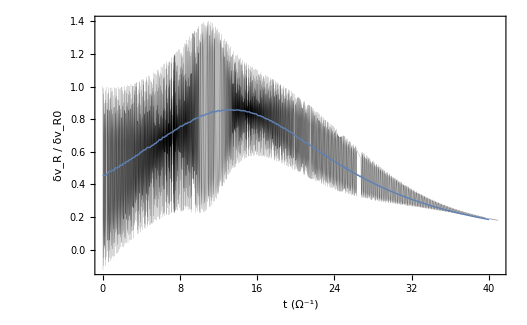

```mathematica
Graphico8=Show[Plot[δvRsol[tref*t]/δvRsol[0],{t,0,(tEnd/tref)/(2*10^3)},PlotStyle->Directive[Black,Thickness[10^-4]],PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)","δv_R / δv_R0 "},BaseStyle->{FontWeight->"Plain",FontSize->14}],ListPlot[Table[{t,meanδvRsol[t*tref]},{t,0,40,0.1}],Joined->True,PlotStyle->Thick]]
```

```mathematica
Show[Plot[δvRsol[tref*t]/δvRsol[0],{t,0,(tEnd/tref)/(2*10^3)},PlotStyle->Directive[Black,Thickness[10^-4]],PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)","δv_R / δv_R0 "},BaseStyle->{FontWeight->"Plain",FontSize->14}],ListPlot[Table[{t,meanδvRsol[t*tref]},{t,0,40,0.1}],Joined->True,PlotStyle->Thick]]
```

```mathematica
meanδvSqsol[t0_]:=1/100 Total[Table[(δvRsol[t0+0.01*k*Ω[Rper,zper]^-1]^2+δvϕsol[t0+0.01*k*Ω[Rper,zper]^-1]^2+δvzsol[t0+0.01*k*Ω[Rper,zper]^-1]^2)/vmod0^2,{k,1,100}]]
```

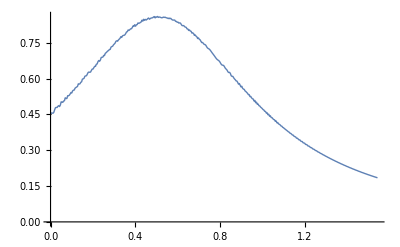

```mathematica
ListPlot[Table[{t,meanδvRsol[t]},{t,0,40 Ω[Rper,zper]^-1,0.1 Ω[Rper,zper]^-1}],Joined->True,PlotStyle->Thick]
```

```mathematica
Table[δvRsol[0+0.001*k*Ω[Rper,zper]^-1],{k,1,100}]
```

{-2.48795,-2.45282,-2.39518,-2.31598,-2.21654,-2.09851,-1.96384,-1.81475,-1.65372,-1.48341,-1.30664,-1.12634,-0.945486,-0.767082,-0.594079,-0.429343,-0.275601,-0.135401,-0.0110652,0.0953458,0.182069,0.247665,0.291049,0.311499,0.308676,0.282625,0.233777,0.16294,0.0712884,-0.0396608,-0.168069,-0.311809,-0.468497,-0.635538,-0.810161,-0.989473,-1.1705,-1.35024,-1.52571,-1.694,-1.85232,-1.99805,-2.12876,-2.2423,-2.33677,-2.4106,-2.46259,-2.49185,-2.49791,-2.48067,-2.44042,-2.37783,-2.29393,-2.19012,-2.06814,-1.93,-1.77801,-1.6147,-1.44277,-1.26509,-1.08461,-0.904344,-0.727281,-0.55637,-0.394454,-0.244228,-0.108192,0.0113887,0.112524,0.193529,0.253056,0.290111,0.304078,0.294722,0.262198,0.207046,0.130184,0.0328908,-0.0832149,-0.2162,-0.363851,-0.523709,-0.693111,-0.869237,-1.04915,-1.22986,-1.40835,-1.58164,-1.74686,-1.90124,-2.04222,-2.16744,-2.27482,-2.36257,-2.42922,-2.47366,-2.49516,-2.49336,-2.46829,-2.42037}

```mathematica
{(17*Pi)/36, 8.744864983216828*^-9, 1.526421860705461*^-10, 
  4.848096202463371*^-9, 1.7695400016431264},
```

```mathematica
θper=17*Pi/36;
ξradiative = (γ-1)*χ ; 
ν=23;  
η=596;    
kR0=8.7*10^-9;
kϕ0=1.52*10^-10;
kz0=4.85*10^-9;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=0.01Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
SolveTheSystem
δvϕsol[t_]:=-(δvRsol[t]*kR[t]+δvzsol[t]*kz[t])/kϕ0
```

{Null}

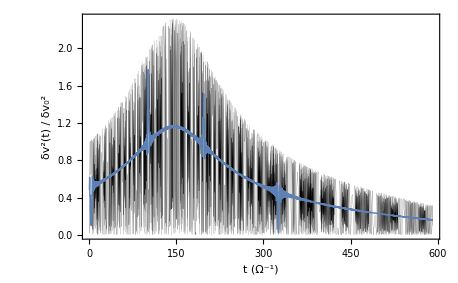

```mathematica
meanδvSqsol[t0_]:=1/200 Total[Table[(δvRsol[t0+0.01*k*Ω[Rper,zper]^-1]^2+δvϕsol[t0+0.01*k*Ω[Rper,zper]^-1]^2+δvzsol[t0+0.01*k*Ω[Rper,zper]^-1]^2)/vmod0^2,{k,1,200}]]

Show[Plot[(δvRsol[tref*t]^2+δvϕsol[t]^2+δvzsol[tref*t]^2)/vmod0^2,{t,0,(tEnd/tref)/(1.5*10^2)},PlotStyle->Directive[Black,Thickness[10^-4]],PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)","δv^2(t) / δv_0^2  "},BaseStyle->{FontWeight->"Plain",FontSize->14}],ListPlot[Table[{t,meanδvSqsol[t*tref]},{t,0,(tEnd/tref)/(1.5*10^2),0.5}],Joined->True,PlotStyle->Thickness[0.2]]]
```